| Estimate | Standard Error | t-Statistic | P-Value
μ | 145.616 | 0.0838263 | 1737.11 | 1.3508×10^-23
σ | 3.33082 | 0.101686 | 32.756 | 8.22764×10^-10
k | 46824.9 | 1118.59 | 41.8606 | 1.16857×10^-10

5608.36 ⅇ^(-0.0450679 (-145.616+x)^2)

| Estimate | Standard Error | t-Statistic | P-Value
μ | 236.12 | 0.0547398 | 4313.49 | 2.11093×10^-41
σ | 4.71449 | 0.0649673 | 72.567 | 2.40518×10^-18
k | 11847.2 | 128.763 | 92.008 | 1.10531×10^-19

1002.52 ⅇ^(-0.0224958 (-236.12+x)^2)

{μ→145.616,σ→3.33082,k→46824.9}

{μ→236.12,σ→4.71449,k→11847.2}

FittedModel[-718.229+8.44159 x]

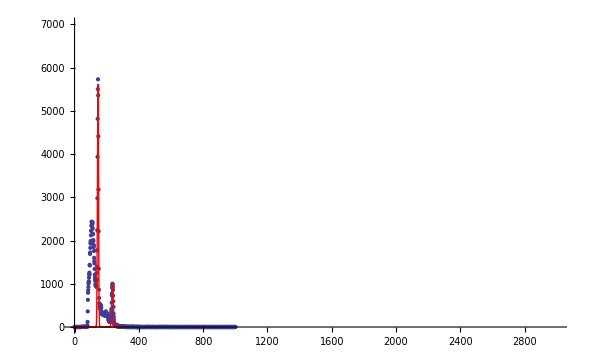

```mathematica
(*Clear unused stuff*)
Clear[ Filename, Filepath, rawBackground, rawData, BackgroundTime, DataTime, removeBackground];

type = "Na";

(*Specify folder structure and filenames*)
Filename = If[type=="Na","Na22-no-bg", "Cs137-1-no-bg"];
Filepath = NotebookDirectory[]<>"../data/";

(*Import raw data from .Spe files*)
rawData = Import[Filepath<> Filename <>".txt", "Table"];
cutData = rawData;

xraypeak = Take[cutData, If[type=="Na", {140,150}, {80,95}]];
gammapeak = Take[cutData, If[type=="Na", {230,245}, {220,240}]];

model[x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));

xrayfitModel=NonlinearModelFit[xraypeak, model[x], {{μ, If[type=="Na",140, 90]}, {σ, 4}, {k, 20000}}, x];
gammafitModel=NonlinearModelFit[gammapeak, model[x], {{μ, 220}, {σ, 8}, {k, 90000}}, x];

xrayfitModel["ParameterTable"]
xrayfitModel["BestFit"]
gammafitModel["ParameterTable"]
gammafitModel["BestFit"]

xrayfit = xrayfitModel["BestFitParameters"]
gammafit = gammafitModel["BestFitParameters"]
xrayTeX = model[x]/.xrayfit;
gammaTeX = model[x]/.gammafit;

ExportString[xrayTeX, "TeX"];
ExportString[gammaTeX, "TeX"];

(* Energy Calibration *)
lit1 =If[type=="Na",511, 32.9];
lit2 =If[type=="Na",1275, 661.66];
DataSet ={{Last[First[xrayfit]], lit1}, {Last[First[gammafit]], lit2}};
calibration=LinearModelFit[DataSet,x,x]

exportName ="Na22-sum-no-bg";
dataToCalibrate = Import[Filepath<> exportName <>".txt", "Table"];
calibratedDate = Select[{calibration[First[#]], Last[#]}&/@dataToCalibrate,First[#]≥-900&];
Export[Filepath<> exportName <>"-calibrated.txt", calibratedDate, "Table"];


Show[{ListPlot[cutData, PlotRange->{{0,300}, {0, 7000}}], Plot[ model[x]/.xrayfit,  {x,0,300}, PlotStyle->Red, PlotRange->{{0,300}, {0, 7000}}],Plot[ model[x]/.gammafit,  {x,0,300}, PlotStyle->Red, PlotRange->{{0,300}, {0, 7000}}]}]
```